# Notebook OctagonalTiling5.nb

## (Version 1.0, 12 January 2005, Uwe Grimm)

## Loading the package

```mathematica
AppendTo[$Path,"/homes/tjakobi/PhD_Work/radialprojection/packages/other"];
AppendTo[$Path,"/homes/tjakobi/PhD_Work/radialprojection/packages"];
```

```mathematica
<<OctagonalTiling.m
```

```mathematica
<<OctagonalTilingCP.m
```

This lists all functions defined in the package:

```mathematica
?AperiodicTilings`OctagonalTiling`*
```

## Projection from four-dimensional hypercubic lattice

### Projetion of the hypercube

Projetion of the hypercube to "physical" ("parallel") and "internal" ("perpendicular","orthogonal") space

```mathematica
?PlotCubeParallelProjection
```

PlotCubeParallelProjection[linethickness,psize,pointcolor,linecolor]
show the projection of the four-dimensional hypercube to parallel
space. The arguments are optional, linethickness determines the width
of lines (default value 1/100), psize the point size (default value 0,
i.e., no points), pointcolor and linecolor the colors of points
(default blue) and lines (default black), respectively. Colors can be
specified either by a single number num, resulting in GrayLevel[num],
or by a list of three of four numbers, in which cases the corresponding 
RGB or CMYK color is used, respectively.

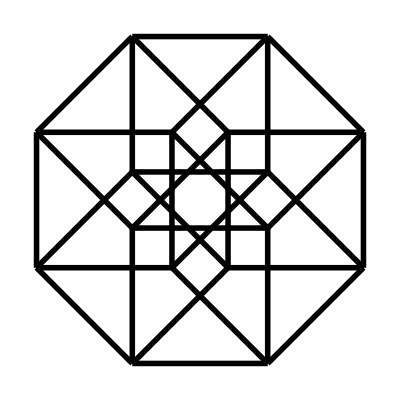

```mathematica
Show[PlotCubeParallelProjection[]]
```

```mathematica
?PlotCubeOrthogonalProjection
```

PlotCubeOrthogonalProjection[linethickness,psize,pointcolor,linecolor]
show the projection of the four-dimensional hypercube to orthogonal
space. The arguments are optional, linethickness determines the width
of lines (default value 1/100), psize the point size (default value 0,
i.e., no points), pointcolor and linecolor the colors of points
(default blue) and lines (default black), respectively. Colors can be
specified either by a single number num, resulting in GrayLevel[num],
or by a list of three of four numbers, in which cases the corresponding 
RGB or CMYK color is used, respectively.

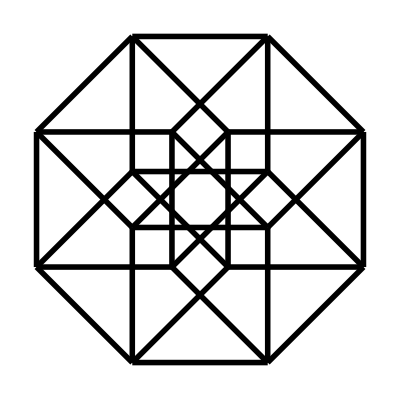

```mathematica
Show[PlotCubeOrthogonalProjection[]]
```

The window for the cut&project set is chosen as the shadow of this projection - thus it is a regular octagon.

### Cut&Project Set

```mathematica
?OctagonalProjectionTiling
```

OctagonalProjectionTiling[initpoint,maxstep] produces a projection
tiling, starting from the initial point initpoint in the
four-dimensional hypercubic lattice and considering all those points
of the lattice that can be reached withing maxstep steps along the
basic lattice vectors. The resulting tiling is returned as a list of
two lists. The first list contains the four-dimensional integer
coordinates of the points in the tiling, the second specifies the
lines that are projections of the basic lattice vectors in the
four-dimensional hypercubic lattice. The lines are encoded in a sorted
list of integers that refer to the position of the projected points
within the first list.

```mathematica
til = OctagonalProjectionTiling[{0,0,0,0},5];
```

constructed patch of octagonal tiling with 73 vertices and 176 bonds

```mathematica
?PlotParallelProjection
```

PlotParallelProjection[{tilingpoints,tilinglines},linethickness,
psize,pointcolor,linecolor] produces graphics for the tiling specified
by tilingpoints and tilinglines. Here, it is assumed that tilingpoints
comprises a list of the four-dimensional integer coordinates of those
lattice points in the hypercubic lattice that belong to the tiling,
and that tilinglines specifies the lines between points by the
positions of the two endpoints in the list tilingpoints. The remaining
arguments are optional, linethickness determines the width of lines
(default value 1/100), psize the point size (default value 0, i.e., no
points), pointcolor and linecolor the colors of points (default blue)
and lines (default black), respectively. Colors can be specified
either by a single number num, resulting in GrayLevel[num], or by a
list of three of four numbers, in which cases the corresponding RGB or
CMYK color is used, respectively.

```mathematica
?PlotOrthogonalProjection
```

PlotOrthogonalProjection[{tilingpoints,tilinglines},linethickness,
psize,pointcolor,linecolor] produces graphics for the projection to
orthogonal space of the tiling specified by tilingpoints and
tilinglines. Here, it is assumed that tilingpoints comprises a list of
the four-dimensional integer coordinates of those lattice points in
the hypercubic lattice that belong to the tiling, and that tilinglines
specifies the lines between points by the positions of the two
endpoints in the list tilingpoints. The projected points and the
acceptance domain are shown. The remaining arguments are optional,
linethickness determines the width of lines (default value 1/100),
psize the point size (default value 1/25), pointcolor and linecolor
the colors of points (default blue) and lines (default black),
respectively. Colors can be specified either by a single number num,
resulting in GrayLevel[num], or by a list of three of four numbers, in
which cases the corresponding RGB or CMYK color is used,
respectively.

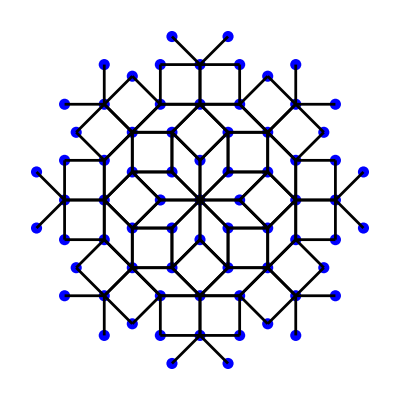

```mathematica
Show[PlotParallelProjection[til,1/200,1/50,{0,0,1}]]
```

```mathematica
?OctagonalInflationPlot
```

OctagonalInflationPlot[tiling,linethickness,psize,showtriangles,
showtrianglelines,showedgedeco,showvertexdeco,pointcolor,linecolor,
rhombcolor,trianglecolor,edgedecocolor,vertexdecocolor] uses
PlotOctagonalTiling to produce graphics for tiling and its inflated
version made by OctagonalInflation. The meaning and default values of
the arguments are the same as in PlotOctagonalTiling.

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

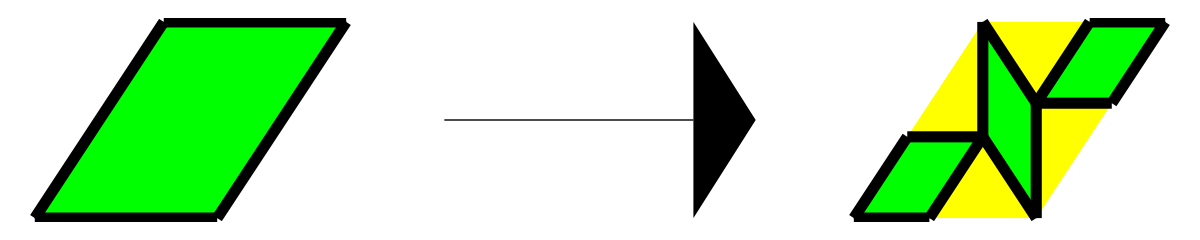

```mathematica
Show[OctagonalInflationPlot[RhombPatch,1/50,0,True]]
```

```mathematica
?OctagonalInflation
```

OctagonalInflation[tiling,n] performs an n-fold inflation of tiling
which has be to a list of triangles and rhombs, which in turn are
specified by three and by four coordinates, respectively. Here, each
coordinate is given as a list of two integers {a,b}, corresponding to
the real number a+b*Sqrt[2], compare TrianglePatch, RhombPatch or
SquarePatch for some examples. In this way, all calculations can be
done with integers. The default value for the number of inflations n
is one.

```mathematica
til0 = OctagonalPatch;
til1 = OctagonalInflation[til0,1];
til2 = OctagonalInflation[til1,1];
til3 = OctagonalInflation[til2,1];
```

```mathematica
?PlotOctagonalTiling
```

PlotOctagonalTiling[tiling,linethickness,psize,showtriangles,
showtrianglelines,showedgedeco,showvertexdeco,pointcolor,linecolor,
rhombcolor,trianglecolor,edgedecocolor,vertexdecocolor] produces
graphics output for an inflation tiling that has to be specified as in
OctagonalInflation, use Show to display the graphics. The argument
linethickness determines the thicknesses of lines, the default values
is 1/100. The argument psize determines the sizes of points
representing the vertices, its default value is 0 (no points). The two
arguments showtriangles and showtrianglelines determine whether
triangles and their edges are shown in the picture, their default
values are False.  Similarly, showedgedeco and showvertexdeco concern
the edge and vertex decorations corresponding to the matching rules,
these are also False by default. The remaining optional arguments
pointcolor, linecolor, rhombcolor, trianglecolor, edgedecocolor, and
vertexdecocolor determine the colors of the various elements, they can
be specified either by a single number num, resulting in
GrayLevel[num], or by a list of three of four numbers, in which cases
the corresponding RGB or CMYK color is used, respectively.

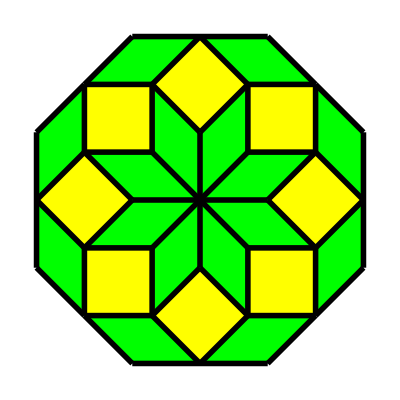

```mathematica
Show[PlotOctagonalTiling[til0]]
```

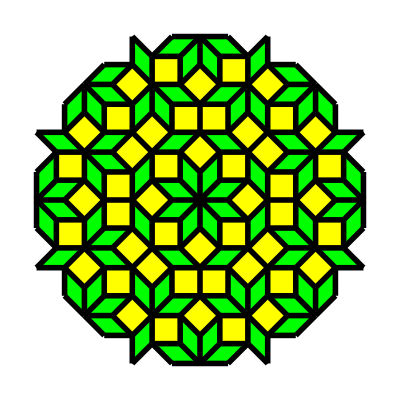

```mathematica
Show[PlotOctagonalTiling[til1]]
```

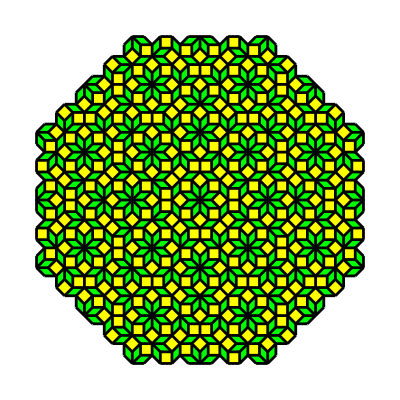

```mathematica
Show[PlotOctagonalTiling[til2,1/200]]
```

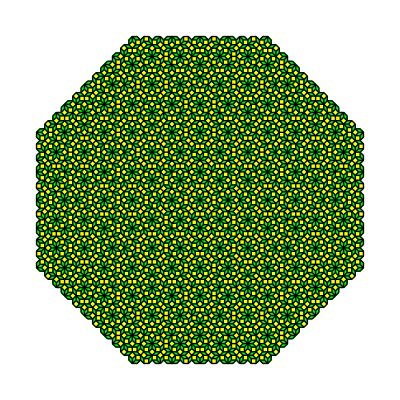

```mathematica
Show[PlotOctagonalTiling[til3,1/400]]
```